```mathematica
2π r
```

```mathematica
x==√((R+h)^2-R^2)
x==√(2 R h + h^2)


R
θ
```

{{x→-√h √(h+2 R)},{x→√h √(h+2 R)}}

R

θ

```mathematica
√(2 6371000*3000+3000^2)//N
```

195538.

```mathematica
R=6371000.;
h=1;
s==ArcCos[R/(R+h)]R//N
```

s==3569.59

```mathematica
sValues={};
xValues={};
For[i=.001,i<4000,i++,{sValues=Append[sValues,ArcCos[R/(R+i)]R],xValues= Append[xValues,i]}]
```

{a→3568.08}

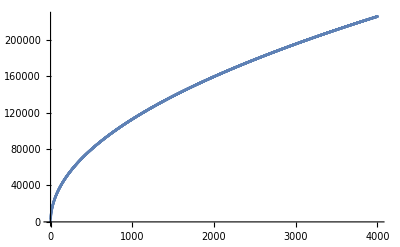

```mathematica
parabola=FindFit[sValues,a √x,{a},x]
Show[{ListPlot[sValues],Plot[a √x/.parabola,{x,0,400}]}]
```

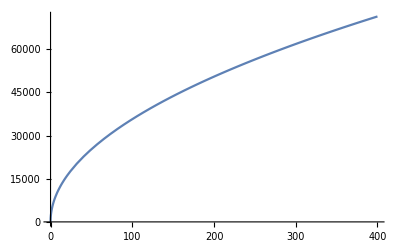

```mathematica
Show[{Plot[a √x/.parabola,{x,0,400}]}]
```